```mathematica
Join[Transpose[Join[{Table[.3,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp3.dat"]][[1]]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp3.dat"]][[2]]}]][[ω*100+1]],Transpose[Join[{Table[.4,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp4.dat"]][[1]]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp4.dat"]][[2]]}]],(*Transpose[Join[{Table[.5,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp5.csv"]][[1]]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp5.csv"]][[2]]}]],*)Transpose[Join[{Table[.6,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp6.dat"]][[1]]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp6.dat"]][[2]]}]],Transpose[Join[{Table[.7,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp7.dat"]][[1]]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp7.dat"]][[2]]}]],Transpose[Join[{Table[.8,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp8.dat"]][[1]]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp8.dat"]][[2]]}]],Transpose[Join[{Table[.9,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp9.dat"]][[1]]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp9.dat"]][[2]]}]]]
```

```mathematica
ListPlot3D[%13]
```

-Graphics3D-

```mathematica
η[ω_]:=Join[Join[{Transpose[Join[{Table[.3,301]},{Table[1,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp3.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.3,301]},{Table[2,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/2imp/2imp3.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.3,301]},{Table[3,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp3.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.3,301]},{Table[4,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/4imp/4imp3.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.3,301]},{Table[5,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/5imp/5imp3.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.3,301]},{Table[6,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/6imp/6imp3.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.3,301]},{Table[7,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/7imp/7imp3.dat"]][[2]]}]][[ω*100+1]]}],
Join[{Transpose[Join[{Table[.4,301]},{Table[1,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp4.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.4,301]},{Table[2,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/2imp/2imp4.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.4,301]},{Table[3,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp4.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.4,301]},{Table[4,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/4imp/4imp4.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.4,301]},{Table[5,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/5imp/5imp4.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.4,301]},{Table[6,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/6imp/6imp4.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.4,301]},{Table[7,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/7imp/7imp4.dat"]][[2]]}]][[ω*100+1]]}],
Join[{Transpose[Join[{Table[.5,401]},{Table[1,401]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp5.csv"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.5,401]},{Table[2,401]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/2imp/2imp5.csv"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.5,401]},{Table[3,401]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp5.csv"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.5,401]},{Table[4,401]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/4imp/4imp5.csv"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.5,401]},{Table[5,401]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/5imp/5imp5.csv"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.5,401]},{Table[6,401]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/6imp/6imp5.csv"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.5,401]},{Table[7,401]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/7imp/7imp5.csv"]][[2]]}]][[ω*100+1]]}],
Join[{Transpose[Join[{Table[.6,301]},{Table[1,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp6.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.6,301]},{Table[2,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/2imp/2imp6.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.6,301]},{Table[3,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp6.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.6,301]},{Table[4,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/4imp/4imp6.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.6,301]},{Table[5,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/5imp/5imp6.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.6,301]},{Table[6,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/6imp/6imp6.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.6,301]},{Table[7,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/7imp/7imp6.dat"]][[2]]}]][[ω*100+1]]}],
Join[{Transpose[Join[{Table[.7,301]},{Table[1,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp7.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.7,301]},{Table[2,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/2imp/2imp7.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.7,301]},{Table[3,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp7.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.7,301]},{Table[4,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/4imp/4imp7.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.7,301]},{Table[5,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/5imp/5imp7.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.7,301]},{Table[6,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/6imp/6imp7.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.7,301]},{Table[7,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/7imp/7imp7.dat"]][[2]]}]][[ω*100+1]]}],
Join[{Transpose[Join[{Table[.8,301]},{Table[1,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp8.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.8,301]},{Table[2,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/2imp/2imp8.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.8,301]},{Table[3,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp8.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.8,301]},{Table[4,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/4imp/4imp8.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.8,301]},{Table[5,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/5imp/5imp8.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.8,301]},{Table[6,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/6imp/6imp8.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.8,301]},{Table[7,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/7imp/7imp8.dat"]][[2]]}]][[ω*100+1]]}],
Join[{Transpose[Join[{Table[.9,301]},{Table[1,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp9.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.9,301]},{Table[2,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/2imp/2imp9.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.9,301]},{Table[3,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp9.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.9,301]},{Table[4,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/4imp/4imp9.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.9,301]},{Table[5,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/5imp/5imp9.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.9,301]},{Table[6,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/6imp/6imp9.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.9,301]},{Table[7,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/7imp/7imp9.dat"]][[2]]}]][[ω*100+1]]}]]
```

```mathematica
aa=η[1.5]
bb=Interpolation[aa]
Plot3D[bb[x,y],{x,0.30,0.9},{y,1.,7.}]
```

{{0.3,1,2.52554},{0.3,2,2.17899},{0.3,3,1.91667},{0.3,4,1.72323},{0.3,5,1.54662},{0.3,6,1.40483},{0.3,7,1.46494},{0.4,1,2.24546},{0.4,2,1.77647},{0.4,3,1.45699},{0.4,4,1.20645},{0.4,5,1.04339},{0.4,6,0.878627},{0.4,7,0.951632},{0.5,1,1.95164},{0.5,2,1.41564},{0.5,3,1.0788},{0.5,4,0.827908},{0.5,5,0.66858},{0.5,6,0.550039},{0.5,7,0.462597},{0.6,1,1.67293},{0.6,2,1.11415},{0.6,3,0.77678},{0.6,4,0.575642},{0.6,5,0.451479},{0.6,6,0.38542},{0.6,7,0.416979},{0.7,1,1.42455},{0.7,2,0.856026},{0.7,3,0.562961},{0.7,4,0.418686},{0.7,5,0.343843},{0.7,6,0.316117},{0.7,7,0.324513},{0.8,1,1.20527},{0.8,2,0.665852},{0.8,3,0.435949},{0.8,4,0.337737},{0.8,5,0.303947},{0.8,6,0.293215},{0.8,7,0.296571},{0.9,1,1.02236},{0.9,2,0.511804},{0.9,3,0.343765},{0.9,4,0.303429},{0.9,5,0.296551},{0.9,6,0.288988},{0.9,7,0.298706}}

InterpolatingFunction[…]

-Graphics3D-

```mathematica
Plot3D[bb[x,y],{x,0.3,0.9},{y,1.,7.},PlotTheme->"Scientific"]
```

-Graphics3D-

```mathematica
Plot3D[bb[x,y],{x,0.3,0.9},{y,1.,7.},PlotStyle->Automatic,PlotTheme->"Scientific"]
```

-Graphics3D-

```mathematica
Graphics3D[PolyhedronData["Dodecahedron","GraphicsComplex"],BoxStyle->Dashing[{0.02,0.02}],Axes->True,AxesStyle->Thickness[0.01]]
```

```mathematica
Plot3D[bb[x,y],{x,0.3,0.9},{y,1.,7.},PlotTheme->"Scientific",PlotStyle->Automatic,BoxStyle->Dashing[{0.01,0.01}],Axes->True(*,AxesStyle->Thickness[0.005]*),AxesLabel->{"ϵ","n","Γ̄"}]
```

-Graphics3D-

```mathematica
Plot3D[bb[x,y],{x,0.3,0.9},{y,1.,7.},Filling->Bottom,PlotStyle->Automatic,PlotTheme->"Scientific"]
```

-Graphics3D-

```mathematica
Plot3D[%13[x,y],{x,0.3,0.9},{y,1.,7.},PlotPoints->160,MaxRecursion->6]
```

-Graphics3D-

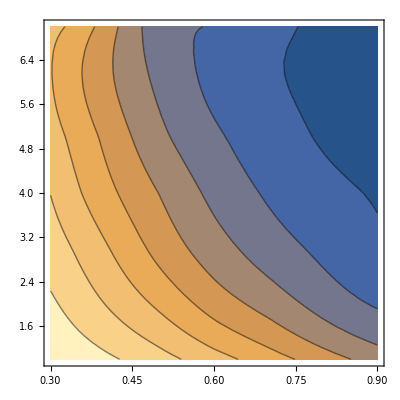

```mathematica
ContourPlot[%11[x,y],{x,0.3,0.9},{y,1.,7.}]
```

```mathematica
η[1.05]
```

```mathematica
{{0.3,1,1.4308238247535023},{0.3,2,0.8357368558297754},{0.3,3,0.5921324093452588},{0.3,4,0.4793923997217612},{0.3,5,0.4170673124361276},{0.3,6,0.40351228021451785},{0.3,7,0.4085428932303708},{0.4,1,0.37408606703523967},{0.4,2,0.336897853862473},{0.4,3,0.3276821545112504},{0.4,4,0.3456746320070247},{0.4,5,0.3444852927892612},{0.4,6,0.3627818772024174},{0.4,7,0.3578844302433902},{0.5,1,0.9241509986235423},{0.5,2,0.48551765828625326},{0.5,3,0.3910261103377603},{0.5,4,0.375295061896211},{0.5,5,0.36374261424354554},{0.5,6,0.3611396179065647},{0.5,7,0.3617879198862075},{0.6,1,1.3646912702962204},{0.6,2,0.7953822178570783},{0.6,3,0.549677968ω703`},{0.6,4,0.4470341186496607},{0.6,5,0.4144685542397116},{0.6,6,0.3836262181321905},{0.6,7,0.40410586602560933},{0.7,1,1.475438362750425},{0.7,2,0.883769906804853},{0.7,3,0.6349665780825752},{0.7,4,0.5017632844630721},{0.7,5,0.4213964803116162},{0.7,6,0.40656740587044776},{0.7,7,0.42453348826023807},{0.8,1,1.4929449963951942},{0.8,2,0.8962885497075606},{0.8,3,0.6182429437188499},{0.8,4,0.4859941263135411},{0.8,5,0.43367071493811876},{0.8,6,0.40875238717797346},{0.8,7,0.42607502630372246},{0.9,1,1.4216225967842762},{0.9,2,0.8510247846217284},{0.9,3,0.5899087997322234},{0.9,4,0.48552346610450975},{0.9,5,0.42956312854938494},{0.9,6,0.4024445593523405},{0.9,7,0.42028288459136204}}
```

```mathematica
ContourPlot[Interpolation[%5][a,y],{a,0.3,0.9},{y,1.,7.}]
```

Interpolation::innd: First argument in InterpolatingFunction[{{0.3,0.9},{1.,7.}},{5,7,0,{7,7},{4,4},0,0,0,0,Automatic,{},{},False},«1»,{Developer`PackedArrayForm,{0,1,«46»,48,49},{2.74296,2.54863,2.36491,2.20154,2.07652,1.96547,2.04573,2.58652,2.2583,2.00625,1.82239,1.66895,1.52405,1.6117,2.39557,1.96898,«17»,0.672441,0.724692,1.80024,1.20914,0.91212,0.724,0.633336,0.553533,0.580751,1.63018,1.0347,0.771748,0.633407,0.553536,0.524451,0.5383}},{Automatic,Automatic}] does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

-Graphics-

```mathematica
ContourPlot[x/Exp[x^2+y^2],{x,-2,2},{y,-2,2},ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&)]
```

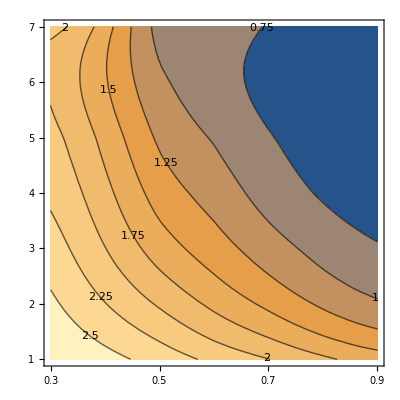

```mathematica
ContourPlot[Interpolation[%24][a,y],{a,0.3,0.9},{y,1.,7.},ContourStyle->Directive[GrayLevel[0],Opacity[0.618]],ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),FrameTicks->{{{1,2,3,4,5,6,7},None},{{0.3,0.5,0.7,0.9},None}}]
```

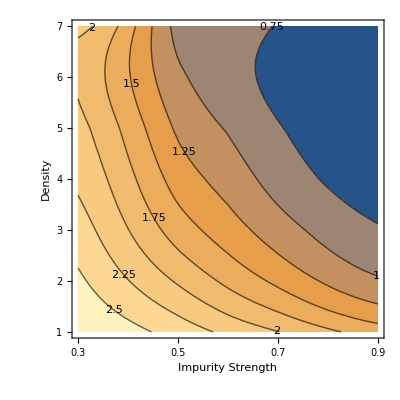

```mathematica
Show[%28,FrameLabel->{{HoldForm[Density],None},{HoldForm[Impurity Strength],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

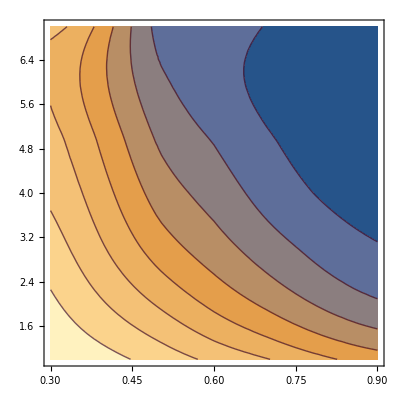

```mathematica
ContourPlot[Interpolation[%2][a,y],{a,0.3,0.9},{y,1.,7.},ContourStyle->Directive[RGBColor[0.21,0.,0.11],Opacity[0.658]]]
```

```mathematica
κ[1.05]
```

$Aborted

```mathematica
q[ω_]:=Join[{Transpose[Join[{Table[.4,301]},{Table[1,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp4.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.4,301]},{Table[2,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/2imp/2imp4.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.4,301]},{Table[3,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp4.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.4,301]},{Table[4,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/4imp/4imp4.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.4,301]},{Table[5,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/5imp/5imp4.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.4,301]},{Table[6,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/6imp/6imp4.dat"]][[2]]}]][[ω*100+1]]},{Transpose[Join[{Table[.4,301]},{Table[7,301]},{Transpose[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/7imp/7imp4.dat"]][[2]]}]][[ω*100+1]]}]
```

```mathematica
q[1]
```

{{0.4,1,2.58652},{0.4,2,2.2583},{0.4,3,2.00625},{0.4,4,1.82239},{0.4,5,1.66895},{0.4,6,1.52405},{0.4,7,1.6117}}

```mathematica
{Transpose[%52][[1]],Transpose[%52][[3]]}
```

{{0.4,0.4,0.4,0.4,0.4,0.4,0.4},{2.58652,2.2583,2.00625,1.82239,1.66895,1.52405,1.6117}}

```mathematica
Transpose[{{1,2,3,4,5,6,7},{2.5865244899260396,2.258303145282934,2.0062518855059395,1.8223921144163595,1.6689514881748138,1.5240517537927072,1.6116985092543463}}]
```

{{1,2.58652},{2,2.2583},{3,2.00625},{4,1.82239},{5,1.66895},{6,1.52405},{7,1.6117}}

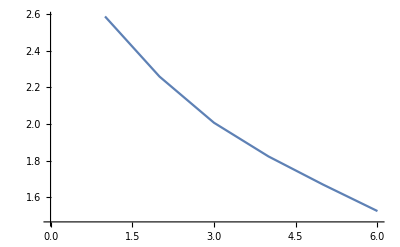

```mathematica
ListPlot[{{1,2.5865244899260396},{2,2.258303145282934},{3,2.0062518855059395},{4,1.8223921144163595},{5,1.6689514881748138},{6,1.5240517537927072}},Joined->True]
```

```mathematica
ListPointPlot3D[{{0.4,1,2.5865244899260396},{0.4,2,2.258303145282934},{0.4,3,2.0062518855059395},{0.4,4,1.8223921144163595},{0.4,5,1.6689514881748138},{0.4,6,1.5240517537927072},{0.4,7,1.6116985092543463}}]
```

-Graphics3D-

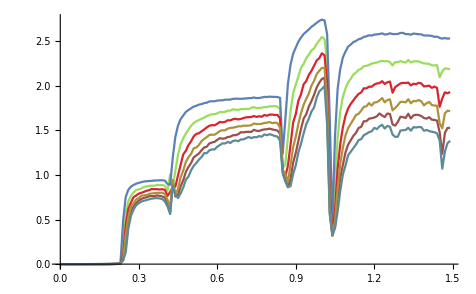

```mathematica
Show[ListLinePlot[k23[[;;150]],PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]],ListLinePlot[k13[[;;150]]],ListLinePlot[k33[[;;150]],PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]],ListLinePlot[k53[[;;150]],PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]],ListLinePlot[k43[[;;150]],PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]],ListLinePlot[k63[[;;150]],PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]],PlotRange->All]
```

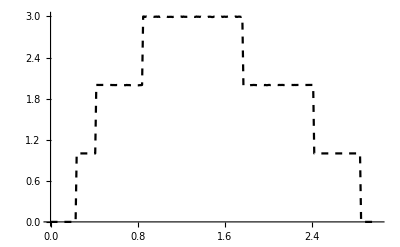

-Graphics-

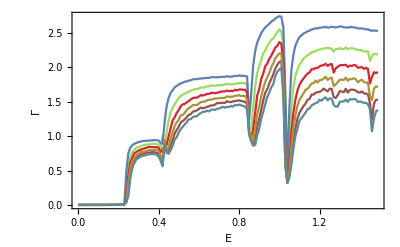

```mathematica
Show[%72,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{HoldForm[Γ̄],None},{HoldForm[Ε],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

```mathematica
k13:=k13=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/14imp100.csv"]
k23:=k23=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/28imp100.csv"]
k33:=k33=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/42imp100.csv"]
k43:=k43=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/56imp100.csv"]
k53:=k53=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/70imp100.csv"]
k63:=k63=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/84imp100.csv"]
k73:=k73=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/100imp100.csv"]
k83:=k83=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/114imp100.csv"]
k93:=k93=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/140imp100.csv"]
```

```mathematica
Join[{3},{k13[[101,2]]},{k23[[101,2]]},{k33[[101,2]]},{k43[[101,2]]},{k53[[101,2]]},{k63[[101,2]]},{k73[[101,2]]},{k83[[101,2]]},{k93[[101,2]]}]
```

{3,2.39557,1.96898,1.63131,1.39113,1.20677,1.04862,0.917215,0.689114,0.554326}

```mathematica
w
```

```mathematica
k53[[95,2]]-3
```

```mathematica
-2.1736585429326554/5
```

-0.434732

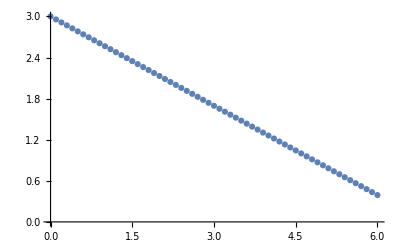

```mathematica
ListPlot[Table[{x,%136*x+3},{x,Range[0,6,0.1]}]]
```

```mathematica
κ1111[ω_]:=Show[ListPlot[Table[{y-1,Join[{3},{k13[[ω,2]]},{k23[[ω,2]]},{k33[[ω,2]]},{k43[[ω,2]]},{k53[[ω,2]]},{k63[[ω,2]]},{k73[[ω,2]]},{k83[[ω,2]]},{k93[[ω,2]]}][[y]]},{y,1,10}],Joined->True,Frame->True,PlotStyle->Red,FrameLabel->{{HoldForm[Γ[Ε=1]],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}],ListPlot[Table[{x,%136*x+3},{x,Range[0,6,0.1]}]]]
```

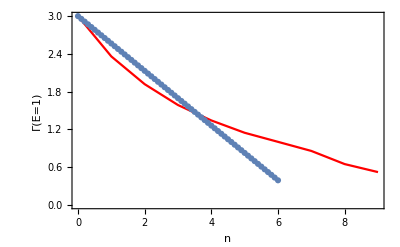

```mathematica
κ1111[100]
```

```mathematica
Manipulate[κ1111[ω],{ω,80,150}]
```

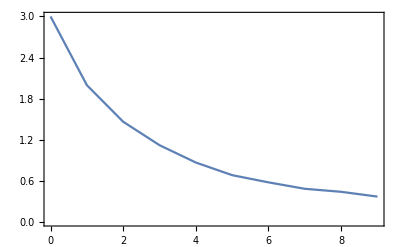

```mathematica
Show[κ1111[140],Frame->True,PlotStyle->Red]
```

```mathematica
Show[%111,FrameLabel->{{HoldForm[Γ[Ε=1]],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

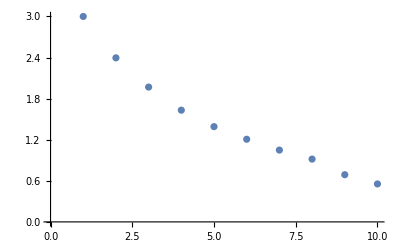

```mathematica
ListPlot[{3,2.3955685818737495,1.968983672580076,1.6313142677856058,1.3911251163408365,1.2067745814733974,1.0486165945874077,0.9172154376594339,0.6891137975321286,0.5543263295996713}]
```

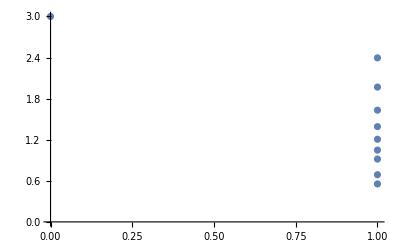

```mathematica
ListPlot[%87]
```

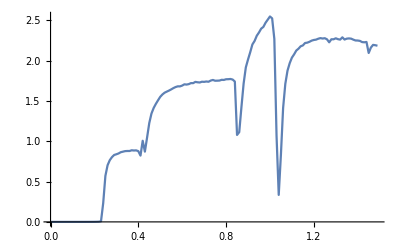

```mathematica
ListLinePlot[k23[[;;150]]]
```